```mathematica
(*No feedback parameters for Fig 1C, Fig 2A*)
p0=0.25;q0=0.2;p1=0.3;q1=0.01;v0=0.5;v1=1;d2=0.05;d0=0.1;d2=1;d1=0.5;
(*Equations for No Feedback*)
equA = (x0'[t]==(p0-q0)*v0*x0[t]-d0*x0[t]);
equB = (x1'[t]==(1-p0+q0)*v0*x0[t]+(p1-q1)*v1*x1[t]-d1*x1[t]);
equC = (x2'[t]==(1-p1+q1)*v1*x1[t]-d2*x2[t]);
(*No feedback figure results*)
initNumCells = 1.5*10^5;
noFeedbackResults = NDSolveValue[{equA,equB,equC,x0[0]==initNumCells,x1[0]==initNumCells,x2[0]==initNumCells},{x0,x1,x2},{t,0,20}];
noFeedbackNumCells[t_]:=noFeedbackResults[[1]][t]+noFeedbackResults[[2]][t]+noFeedbackResults[[3]][t];
```

```mathematica
(*Equations for Type I feedback*)
```

```mathematica
p0=0.5;q0=0.2;p1=0.5;q1=0.1;v0=0.5;v1=1;d2=0.05;d0=0.1;d1=0.5;d2=1;beta0=2*10^-11;beta1=3*10^-12; tau=2;
equ0=(x0'[t]==(p0-q0)(v0/(1+beta0*(x2[t-tau])^2))*x0[t]-d0*x0[t]);
equ1 = (x1'[t]==(1-p0+q0)*(v0/(1+beta0*(x2[t-tau])^2))*x0[t]+(p1-q1)(v1/(1+beta1*(x2[t-tau])^2))*x1[t]-d1*x1[t]);
equ2 = (x2'[t]==(1-p1+q1)(v1/(1+beta1*(x2[t-tau])^2))*x1[t]-d2*x2[t]);
typeIfeedbackResults = NDSolveValue[{equ0,equ1,equ2,x0[0]==initNumCells,x1[0]==initNumCells,x2[0]==initNumCells},{x0,x1,x2},{t,0,20}]
typeIfeedbackNumCells[t_]:=typeIfeedbackResults[[1]][t]+typeIfeedbackResults[[2]][t]+typeIfeedbackResults[[3]][t];
```

NDSolveValue::ihist: Conditions given at t = 0. will be interpreted as initial history functions for t/;t≤0..

{InterpolatingFunction[{{0., 20.}}, <>],InterpolatingFunction[{{0., 20.}}, <>],InterpolatingFunction[{{0., 20.}}, <>]}

```mathematica
(*Equations for Type II feedback*)
```

```mathematica
p0=0.5;q0=0.2;p1=0.5;q1=0.1;v0=0.5;v1=1;d2=0.05;d0=0.1;d1=0.5;d2=1;tau=2; gamma10=5*10^-14; gamma20 = 7 * 10^-15; gamma11 = 6*10^-13; gamma21 = 2*10^-15;

equ3 = (x0'[t]==(p0/(1+gamma10*(x2[t-tau])^2) - q0/(1+gamma20*(x2[t-tau])^2))*v0*x0[t]-d0*x0[t]);
equ4 = (x1'[t]==(p0/(1+gamma10*(x2[t-tau])^2) - q0/(1+gamma20*(x2[t-tau])^2))*v0*x0[t] + (p0/(1+gamma11*(x2[t-tau])^2) - q0/(1+gamma21*(x2[t-tau])^2))*v1*x1[t]-d1*x1[t]);
equ5 = (x2'[t]==(1-p1/(1+gamma11*(x2[t-tau])^2) + q1/(1+gamma21*(x2[t-tau])^2))*v1*x1[t]-d2*x2[t]);
typeIIfeedbackResults = NDSolveValue[{equ3,equ4,equ5,x0[0]==initNumCells,x1[0]==initNumCells,x2[0]==initNumCells},{x0,x1,x2},{t,0,20}]
typeIIfeedbackNumCells[t_]:=typeIIfeedbackResults[[1]][t]+typeIIfeedbackResults[[2]][t]+typeIIfeedbackResults[[3]][t];
```

NDSolveValue::ihist: Conditions given at t = 0. will be interpreted as initial history functions for t/;t≤0..

{InterpolatingFunction[{{0., 20.}}, <>],InterpolatingFunction[{{0., 20.}}, <>],InterpolatingFunction[{{0., 20.}}, <>]}

```mathematica
(*Equation for Type I and Type II together*)
```

```mathematica
p0=0.5;q0=0.2;p1=0.5;q1=0.1;v0=0.5;v1=1;d2=0.05;d0=0.1;d1=0.5;d2=1;tau=2; gamma10=10^-14; gamma20 = 10^-16; gamma11 = 10^-13; gamma21 = 10^-15;
beta0=8*10^-12; beta1=4*10^-13;
equ6 = (x0'[t]==(p0/(1+gamma10*(x2[t-tau])^2) - q0/(1+gamma20*(x2[t-tau])^2))*(v0/(1+beta0*(x2[t-tau])^2))*x0[t]-d0*x0[t]);
equ7 = (x1'[t]==(1-p0/(1+gamma10*(x2[t-tau])^2) + q0/(1+gamma20*(x2[t-tau])^2))*(v0/(1+beta0*(x2[t-tau])^2))*x0[t]+(p1/(1+gamma11*(x2[t-tau])^2) + q1/(1+gamma21*(x2[t-tau])^2))*(v1/(1+beta1*(x2[t-tau])^2))*x1[t]-d1*x1[t]);
equ8 = (x2'[t]==(1-p1/(1+gamma11*(x2[t-tau])^2) + q1/(1+gamma21*(x2[t-tau])^2))*(v1/(1+beta1*(x2[t-tau])^2))*x1[t]-d2*x2[t]);
typeIandIIfeedbackResults = NDSolveValue[{equ6,equ7,equ8,x0[0]==initNumCells,x1[0]==initNumCells,x2[0]==initNumCells},{x0,x1,x2},{t,0,20}]
typeIandIIfeedbackNumCells[t_]:=typeIandIIfeedbackResults[[1]][t]+typeIandIIfeedbackResults[[2]][t]+typeIandIIfeedbackResults[[3]][t];
```

NDSolveValue::ihist: Conditions given at t = 0. will be interpreted as initial history functions for t/;t≤0..

{InterpolatingFunction[{{0., 20.}}, <>],InterpolatingFunction[{{0., 20.}}, <>],InterpolatingFunction[{{0., 20.}}, <>]}

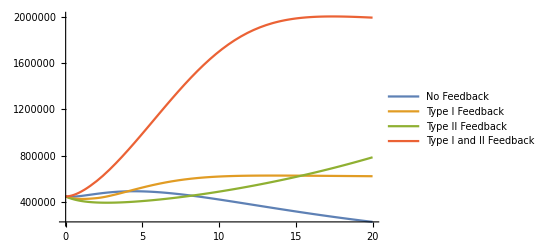

```mathematica
(*Figure 1C Attempt*)
Plot[{noFeedbackNumCells[t],typeIfeedbackNumCells[t],typeIIfeedbackNumCells[t],typeIandIIfeedbackNumCells[t]},{t,0,20},PlotLegends->{"No Feedback","Type I Feedback","Type II Feedback","Type I and II Feedback"}]
```

NDSolveValue::ihist: Conditions given at t = 0. will be interpreted as initial history functions for t/;t≤0..

{InterpolatingFunction[{{0., 120.}}, <>],InterpolatingFunction[{{0., 120.}}, <>],InterpolatingFunction[{{0., 120.}}, <>]}

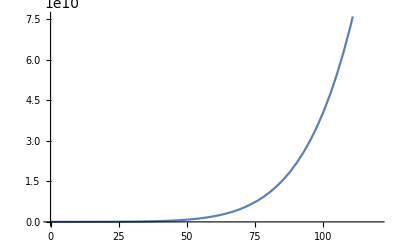

```mathematica
(*Figure 1D Attempt*)
p0=0.5;q0=0.2;p1=0.5;q1=0.1;v0=0.5;v1=1;d2=0.05;d0=0.1;d1=0.5;d2=1;tau=2; gamma10=10^-23; gamma20 = 2*10^-24; gamma11 = 4*10^-22; gamma21 =5* 10^-23;
beta0=8*10^-27; beta1=4*10^-27;
initNumCells = 5 * 10^5;
equ10 = (x0'[t]==(p0/(1+gamma10*(x2[t-tau])^2) - q0/(1+gamma20*(x2[t-tau])^2))*(v0/(1+beta0*(x2[t-tau])^2))*x0[t]-d0*x0[t]);
equ11 = (x1'[t]==(1-p0/(1+gamma10*(x2[t-tau])^2) + q0/(1+gamma20*(x2[t-tau])^2))*(v0/(1+beta0*(x2[t-tau])^2))*x0[t]+(p1/(1+gamma11*(x2[t-tau])^2) + q1/(1+gamma21*(x2[t-tau])^2))*(v1/(1+beta1*(x2[t-tau])^2))*x1[t]-d1*x1[t]);
equ12 = (x2'[t]==(1-p1/(1+gamma11*(x2[t-tau])^2) + q1/(1+gamma21*(x2[t-tau])^2))*(v1/(1+beta1*(x2[t-tau])^2))*x1[t]-d2*x2[t]);
fig1DsimResults = NDSolveValue[{equ10,equ11,equ12,x0[0]==initNumCells,x1[0]==initNumCells,x2[0]==initNumCells},{x0,x1,x2},{t,0,120}]
typeIandIIfeedbackNumCells[t_]:=typeIandIIfeedbackResults[[1]][t]+typeIandIIfeedbackResults[[2]][t]+typeIandIIfeedbackResults[[3]][t];
Plot[typeIandIIfeedbackNumCells[t],{t,0,120}]
```